### Schrodinger equation

```mathematica
{100.35409971057244,100.83693058231086,101.17025105623021,101.47730166184346,101.74510602677982,102.0009736026827,102.235829637388,102.46334617258368,102.67707551793126,102.88564643258681,103.08419917486967,103.27884023045809}
%-100
(*m=25/.m1=50,m2=50*)
```

{100.354,100.837,101.17,101.477,101.745,102.001,102.236,102.463,102.677,102.886,103.084,103.279}

{0.3541,0.836931,1.17025,1.4773,1.74511,2.00097,2.23583,2.46335,2.67708,2.88565,3.0842,3.27884}

```mathematica
{200.28672350055405,200.67046225355503,200.9352536891997,201.17941851671853,201.39232860805592,201.5959131173006,201.78274642599806,201.9638694035673,202.1339901240336,202.30011189710405,202.45823212617213,202.61332974090902}-200
```

{0.286724,0.670462,0.935254,1.17942,1.39233,1.59591,1.78275,1.96387,2.13399,2.30011,2.45823,2.61333}

```mathematica
{1000.1714591057114,1000.3960497724252,1000.5509825585149,1000.6939299177724,1000.8185629681388,1000.9377961268883,1001.0472285870462,1001.1534951401695,1001.253979006189,1001.3541617060578,1001.4548855673336,1001.56152690631}-1000
```

{0.171459,0.39605,0.550983,0.69393,0.818563,0.937796,1.04723,1.1535,1.25398,1.35416,1.45489,1.56153}

```mathematica
m=250;
λ=π/2;
```

```mathematica
Print["Even"];
tabE=Module[{r1=100,r2},
r2=0;
NDEigenvalues[{-f''[x]/(2m)+λ Abs[x]f[x](*,DirichletCondition[f[x]==0,True]*)},f,{x,r2,r1},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]]
Print["Odd"];
tabO=Module[{r1=100,r2},
r2=0;
NDEigenvalues[{-f''[x]/(2m)+λ Abs[x]f[x],DirichletCondition[f[x]==0,True]},f,{x,r2,r1},3,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]]
tab=Riffle[tabE,tabO]
tab2=Module[{r1=100,r2},
r2=-r1;
NDEigenvalues[{-f''[x]/5+π/2 Abs[x]f[x]},f,{x,r2,r1},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]]
```

Even

{0.173451,0.553009,0.820627}

Odd

{0.398065,0.695978,0.939882}

{0.173451,0.398065,0.553009,0.695978,0.820627,0.939882}

{0.805086,1.84766,2.56684,3.23044,3.80901,4.36254,4.87046,5.3631,5.82576,6.27774,6.7079,7.13002,7.53525,7.9341,8.31933,8.69933,9.068,9.43226,9.7869,10.1378,10.4803,10.8195,11.1514,11.4804,11.8029,12.1228,12.4369,12.7486,13.0551,13.3594,13.659,13.9566,14.2498,14.5412,14.8286,15.1143,15.3963,15.6768,15.9538,16.2293,16.5016,16.7726,17.0406,17.3072,17.5711,17.8337,18.0937,18.3526,18.6089,18.8642}

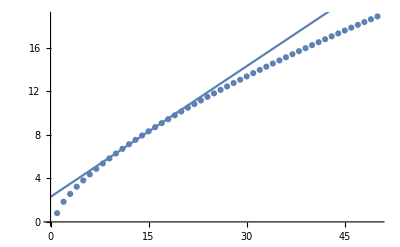

```mathematica
Show[ListPlot[tab2],Plot[0.4x+2.3,{x,0,50}]]
```

```mathematica
r1=100;
r2=-r1;
min=10^-6;
```

```mathematica
sol1=ParametricNDSolve[{-f''[x]/2+Abs[x]f[x]==e f[x],f[r1]==min,f'[r1]==-min},f,{x,r2,r1},e];
FindRoot[f[e][r2]==min/.sol1,{e,1,2}]
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→1.85576}

InterpolatingFunction[{{-100., 100.}}, <>][x]

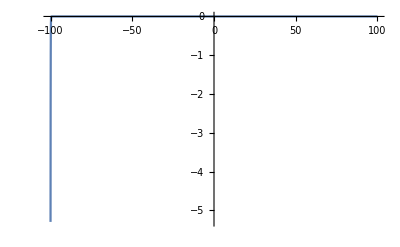

```mathematica
f[e][x]/.sol1/.%53
NIntegrate[%^2,{x,r2,r1}];
Plot[%%/√%,{x,r2,r1},PlotRange->All]
```

### Relativity correction

```mathematica
sol2=ParametricNDSolve[{-f''[x]+2Abs[x]f[x]-(e-Abs[x])^2/4 f[x]==2e f[x],f[r1]==min,f'[r1]==-min},f,{x,r2,r1},e,MaxSteps->Infinity]
FindRoot[f[e][r2]==min/.sol2,{e,1,1.3}]
```

{f→ParametricFunction[<>]}

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→1.09491}

```mathematica
FindRoot[f[e][r2]==min/.sol2,{e,1.6,2.5}]
```

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→1.8543}

```mathematica
0.8*tab[[1]]
```

0.646893

```mathematica
f[e][x]/.sol2/.%
```

InterpolatingFunction[{{-100., 100.}}, <>][x]

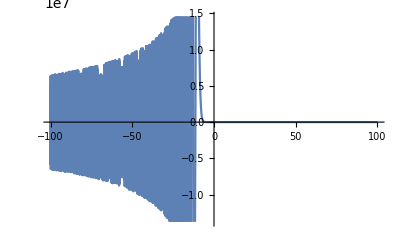

```mathematica
Plot[%46,{x,-100.,100.}]
```

```mathematica
sol2=ParametricNDSolve[{-f''[x]/2+Abs[x]f[x]-f''''[x]/32==e f[x],f[r1]==min,f'[r1]==-min,f'[r2]==-min,f''[r1]==min},f,{x,r2,r1},e,MaxSteps->Infinity]
FindRoot[f[e][r2]==min/.sol2,{e,1,1.8}]
```

{f→ParametricFunction[<>]}

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::berr: 1.94702365531662×10^449 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

ParametricNDSolve::ndsz: 在 x$109829 == -100. 处，步长实际上为零；可能存在奇点或者刚性系统.

ParametricNDSolve::berr: 2.92652394698222×10^443 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

ParametricNDSolve::bvluc: 从边界条件导出的方程在数值上是病态的. 边界条件对于唯一定义一个解可能不是充分的. 如果计算解，那么得到的解可能与边界条件匹配度不佳.

General::stop: 在本次计算中，ParametricNDSolve::bvluc 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x$109829 == -100. 处，步长实际上为零；可能存在奇点或者刚性系统.

ParametricNDSolve::berr: 6.60089020370813×10^443 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，ParametricNDSolve::berr 的进一步输出将被抑制.

ParametricNDSolve::ndsz: 在 x$109829 == -100. 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，ParametricNDSolve::ndsz 的进一步输出将被抑制.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

{e→1.73639}

### Analytic

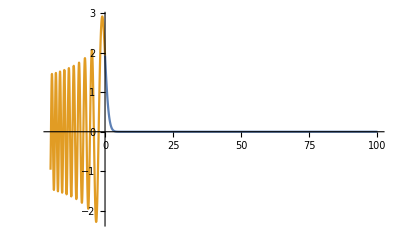

```mathematica
Plot[{√x BesselK[1/3,2/3 x^(3/2)],π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)])&&x<0},{x,-20,100},PlotRange->All]
```

```mathematica
Limit[√x BesselK[1/3,2/3 x^(3/2)],x->0]
```

π/(3^(1/6) Gamma[2/3])

```mathematica
Limit[π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]),x->0]
```

π/(3^(1/6) Gamma[2/3])

```mathematica
Print["Odd"]
```

Odd

```mathematica
FindRoot[π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)])==0/.x->-2^(1/3)e,{e,10,11}]
```

{e→14.605}

```mathematica
Print["Even"]
```

Even

```mathematica
D[π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]),x]
```

(π (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]) Abs'[x])/(2 √3 √Abs[x])+1/(√3)π √Abs[x] (1/2 √Abs[x] (BesselJ[-4/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]) Abs'[x]+1/2 √Abs[x] (BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs'[x])

```mathematica
Simplify[%190]
```

1/(2 √3 √Abs[x])π (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]+Abs[x]^(3/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)])) Abs'[x]

```mathematica
FindRoot[1/(2 √3 √Abs[x])π (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]+Abs[x]^(3/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)])) (*Abs[x]*)==0/.x->-2^(1/3)e,{e,0.1,1}]
```

{e→0.808617}

```mathematica
Evaluate@D[π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]),{x,2}]
```

1/(√3)π (1/(√Abs[x])Abs'[x] (1/2 √Abs[x] (BesselJ[-4/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]) Abs'[x]+1/2 √Abs[x] (BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs'[x])+(BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]) (-Abs'[x]^2/(4 Abs[x]^(3/2))+Abs''[x]/(2 √Abs[x]))+√Abs[x] (((BesselJ[-4/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]) Abs'[x]^2)/(4 √Abs[x])+((BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs'[x]^2)/(4 √Abs[x])+1/2 √Abs[x] Abs'[x] (1/2 √Abs[x] (BesselJ[-7/3,2/3 Abs[x]^(3/2)]-BesselJ[-1/3,2/3 Abs[x]^(3/2)]) Abs'[x]-1/2 √Abs[x] (BesselJ[-1/3,2/3 Abs[x]^(3/2)]-BesselJ[5/3,2/3 Abs[x]^(3/2)]) Abs'[x])+1/2 √Abs[x] Abs'[x] (1/2 √Abs[x] (BesselJ[-5/3,2/3 Abs[x]^(3/2)]-BesselJ[1/3,2/3 Abs[x]^(3/2)]) Abs'[x]-1/2 √Abs[x] (BesselJ[1/3,2/3 Abs[x]^(3/2)]-BesselJ[7/3,2/3 Abs[x]^(3/2)]) Abs'[x])+1/2 √Abs[x] (BesselJ[-4/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]) Abs''[x]+1/2 √Abs[x] (BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs''[x]))

```mathematica
Simplify[%217]
```

```mathematica
1/(4 √3 Abs[x]^(3/2))π (-(BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]) Abs'[x]^2+3 Abs[x]^(3/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs'[x]^2+Abs[x]^3 (BesselJ[-7/3,2/3 Abs[x]^(3/2)]+BesselJ[-5/3,2/3 Abs[x]^(3/2)]-2 BesselJ[-1/3,2/3 Abs[x]^(3/2)]-2 BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[5/3,2/3 Abs[x]^(3/2)]+BesselJ[7/3,2/3 Abs[x]^(3/2)]) Abs'[x]^2+2 Abs[x] (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]) Abs''[x]+2 Abs[x]^(5/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)]) Abs''[x])/.{Abs[x]->-x,Abs'[x]->-1,Abs''[x]->0}
```

1/(4 √3 (-x)^(3/2))π (-BesselJ[-1/3,2/3 (-x)^(3/2)]-BesselJ[1/3,2/3 (-x)^(3/2)]+3 (-x)^(3/2) (BesselJ[-4/3,2/3 (-x)^(3/2)]+BesselJ[-2/3,2/3 (-x)^(3/2)]-BesselJ[2/3,2/3 (-x)^(3/2)]-BesselJ[4/3,2/3 (-x)^(3/2)])-x^3 (BesselJ[-7/3,2/3 (-x)^(3/2)]+BesselJ[-5/3,2/3 (-x)^(3/2)]-2 BesselJ[-1/3,2/3 (-x)^(3/2)]-2 BesselJ[1/3,2/3 (-x)^(3/2)]+BesselJ[5/3,2/3 (-x)^(3/2)]+BesselJ[7/3,2/3 (-x)^(3/2)]))

```mathematica
2^(4/3)/8 ss Table[Integrate[(D[√x BesselK[1/3,2/3 x^(3/2)],{x,2}])^2,{x,0,∞}]+NIntegrate[(1/(4 √3 (-x)^(3/2))π (-BesselJ[-1/3,2/3 (-x)^(3/2)]-BesselJ[1/3,2/3 (-x)^(3/2)]+3 (-x)^(3/2) (BesselJ[-4/3,2/3 (-x)^(3/2)]+BesselJ[-2/3,2/3 (-x)^(3/2)]-BesselJ[2/3,2/3 (-x)^(3/2)]-BesselJ[4/3,2/3 (-x)^(3/2)])-x^3 (BesselJ[-7/3,2/3 (-x)^(3/2)]+BesselJ[-5/3,2/3 (-x)^(3/2)]-2 BesselJ[-1/3,2/3 (-x)^(3/2)]-2 BesselJ[1/3,2/3 (-x)^(3/2)]+BesselJ[5/3,2/3 (-x)^(3/2)]+BesselJ[7/3,2/3 (-x)^(3/2)])))^2,{x,-2^(1/3)tab2[[i]],0}],{i,6}]
```

{0.0935698,0.328505,0.702734,1.15014,1.67769,2.25969}

```mathematica
(*2^(-1/3)*)ss=1/√Table[Integrate[(√x BesselK[1/3,2/3 x^(3/2)])^2,{x,0,∞}]+Integrate[(π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]))^2,{x,-2^(1/3)tab2[[i]],0}]-Integrate[(π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]))^2,{x,-2*2^(1/3)tab2[[i]],-2^(1/3)tab2[[i]]}]-Integrate[(√-x BesselK[1/3,2/3 Abs[x]^(3/2)])^2,{x,-2*2^(1/3)tab2[[i]],-∞}],{i,6}]
```

{0.588393,0.332207,0.32641,0.294612,0.289881,0.276771}

```mathematica
ss Table[Integrate[(√x BesselK[1/3,2/3 x^(3/2)])^2 2^(-1/3)(x+tab2[[i]]),{x,0,∞}]+Integrate[(π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)]))^2 Abs[2^(-1/3)(x+tab2[[i]])],{x,-2^(1/3)tab2[[i]],0}],{i,6}]
```

{2.06982,4.16431,7.02891,8.66822,11.1041,12.9612}

```mathematica
-1/2 ss Table[Integrate[(D[√x BesselK[1/3,2/3 x^(3/2)],{x,1}])^2,{x,0,∞}]+NIntegrate[(1/(2 √3 √Abs[x])π (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]+Abs[x]^(3/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)])))^2,{x,-2^(1/3)tab2[[i]],0}],{i,6}]
```

{-0.499545,-1.48687,-2.22461,-2.97742,-3.65083,-4.33173}

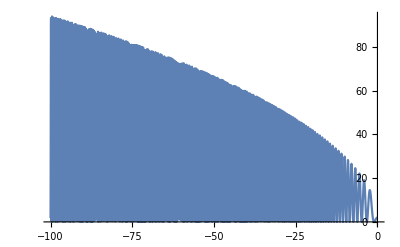

```mathematica
Plot[(1/(2 √3 √Abs[x])π (BesselJ[-1/3,2/3 Abs[x]^(3/2)]+BesselJ[1/3,2/3 Abs[x]^(3/2)]+Abs[x]^(3/2) (BesselJ[-4/3,2/3 Abs[x]^(3/2)]+BesselJ[-2/3,2/3 Abs[x]^(3/2)]-BesselJ[2/3,2/3 Abs[x]^(3/2)]-BesselJ[4/3,2/3 Abs[x]^(3/2)])))^2,{x,-100,0}]
```

```mathematica
π/(√3)√Abs[x](BesselJ[1/3,2/3 Abs[x]^(3/2)]+BesselJ[-1/3,2/3 Abs[x]^(3/2)])/.x->2^(1/3)(x-e)
```

1/(√3)2^(1/6) π √Abs[-e+x] (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)])

```mathematica
√x BesselK[1/3,2/3 x^(3/2)]/.x->2^(1/3)(x-e)
```

2^(1/6) √(-e+x) BesselK[1/3,2/3 √2 (-e+x)^(3/2)]

```mathematica
ψ[x_,e_]:=If[x>0,If[x>e,2^(1/6) √(-e+x) BesselK[1/3,2/3 √2 (-e+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-e+x] (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)])],If[x>-e,-1/(√3)2^(1/6) π √Abs[-e-x] (BesselJ[-1/3,2/3 √2 Abs[-e-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e-x]^(3/2)]),-2^(1/6) √(-e-x) BesselK[1/3,2/3 √2 (-e-x)^(3/2)]]]
```

```mathematica
Plot[ψ[x,tab2[[1]]],{x,-1,1}]
```

```mathematica
norm=1/(√(Integrate[ψ[x,#]^2,{x,-∞,+∞}]&/@Take[tab2,6]))
```

{1/(√(∫_(-∞)^∞ If[x>0,If[x>0.808617,2^(1/6) √(-0.808617+x) BesselK[1/3,2/3 √2 (-0.808617+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-0.808617+x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617+x]^(3/2)])],If[x>-0.808617,-1/(√3)2^(1/6) π √Abs[-0.808617-x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]),-2^(1/6) √(-0.808617-x) BesselK[1/3,2/3 √2 (-0.808617-x)^(3/2)]]]^2 ⅆx)),1/(√(∫_(-∞)^∞ If[x>0,If[x>1.85576,2^(1/6) √(-1.85576+x) BesselK[1/3,2/3 √2 (-1.85576+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-1.85576+x] (BesselJ[-1/3,2/3 √2 Abs[-1.85576+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-1.85576+x]^(3/2)])],If[x>-1.85576,-1/(√3)2^(1/6) π √Abs[-1.85576-x] (BesselJ[-1/3,2/3 √2 Abs[-1.85576-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-1.85576-x]^(3/2)]),-2^(1/6) √(-1.85576-x) BesselK[1/3,2/3 √2 (-1.85576-x)^(3/2)]]]^2 ⅆx)),1/(√(∫_(-∞)^∞ If[x>0,If[x>2.5781,2^(1/6) √(-2.5781+x) BesselK[1/3,2/3 √2 (-2.5781+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-2.5781+x] (BesselJ[-1/3,2/3 √2 Abs[-2.5781+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-2.5781+x]^(3/2)])],If[x>-2.5781,-1/(√3)2^(1/6) π √Abs[-2.5781-x] (BesselJ[-1/3,2/3 √2 Abs[-2.5781-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-2.5781-x]^(3/2)]),-2^(1/6) √(-2.5781-x) BesselK[1/3,2/3 √2 (-2.5781-x)^(3/2)]]]^2 ⅆx)),1/(√(∫_(-∞)^∞ If[x>0,If[x>3.24461,2^(1/6) √(-3.24461+x) BesselK[1/3,2/3 √2 (-3.24461+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-3.24461+x] (BesselJ[-1/3,2/3 √2 Abs[-3.24461+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.24461+x]^(3/2)])],If[x>-3.24461,-1/(√3)2^(1/6) π √Abs[-3.24461-x] (BesselJ[-1/3,2/3 √2 Abs[-3.24461-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.24461-x]^(3/2)]),-2^(1/6) √(-3.24461-x) BesselK[1/3,2/3 √2 (-3.24461-x)^(3/2)]]]^2 ⅆx)),1/(√(∫_(-∞)^∞ If[x>0,If[x>3.82572,2^(1/6) √(-3.82572+x) BesselK[1/3,2/3 √2 (-3.82572+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-3.82572+x] (BesselJ[-1/3,2/3 √2 Abs[-3.82572+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.82572+x]^(3/2)])],If[x>-3.82572,-1/(√3)2^(1/6) π √Abs[-3.82572-x] (BesselJ[-1/3,2/3 √2 Abs[-3.82572-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.82572-x]^(3/2)]),-2^(1/6) √(-3.82572-x) BesselK[1/3,2/3 √2 (-3.82572-x)^(3/2)]]]^2 ⅆx)),1/(√(∫_(-∞)^∞ If[x>0,If[x>4.38167,2^(1/6) √(-4.38167+x) BesselK[1/3,2/3 √2 (-4.38167+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-4.38167+x] (BesselJ[-1/3,2/3 √2 Abs[-4.38167+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-4.38167+x]^(3/2)])],If[x>-4.38167,-1/(√3)2^(1/6) π √Abs[-4.38167-x] (BesselJ[-1/3,2/3 √2 Abs[-4.38167-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-4.38167-x]^(3/2)]),-2^(1/6) √(-4.38167-x) BesselK[1/3,2/3 √2 (-4.38167-x)^(3/2)]]]^2 ⅆx))}

```mathematica
Integrate[ψ[x,tab2[[1]]]^2,{x,-∞,+∞}]
```

∫_(-∞)^∞ If[x>0,If[x>0.808617,2^(1/6) √(-0.808617+x) BesselK[1/3,2/3 √2 (-0.808617+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-0.808617+x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617+x]^(3/2)])],If[x>-0.808617,-1/(√3)2^(1/6) π √Abs[-0.808617-x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]),-2^(1/6) √(-0.808617-x) BesselK[1/3,2/3 √2 (-0.808617-x)^(3/2)]]]^2 ⅆx

```mathematica
norm=1/(√(NIntegrate[ψ[x,#]^2,{x,-100,+100}]&/@Take[tab2,6]))
```

{0.269784,0.208016,0.19315,0.181623,0.174651,0.168588}

```mathematica
Table[norm[[i]]Integrate[ψ[x,tab2[[i]]]^2 Abs[x],{x,-∞,+∞}],{i,6}]
```

{0.269784 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>0.808617,2^(1/6) √(-0.808617+x) BesselK[1/3,2/3 √2 (-0.808617+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-0.808617+x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617+x]^(3/2)])],If[x>-0.808617,-1/(√3)2^(1/6) π √Abs[-0.808617-x] (BesselJ[-1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-0.808617-x]^(3/2)]),-2^(1/6) √(-0.808617-x) BesselK[1/3,2/3 √2 (-0.808617-x)^(3/2)]]]^2ⅆx,0.208016 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>1.85576,2^(1/6) √(-1.85576+x) BesselK[1/3,2/3 √2 (-1.85576+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-1.85576+x] (BesselJ[-1/3,2/3 √2 Abs[-1.85576+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-1.85576+x]^(3/2)])],If[x>-1.85576,-1/(√3)2^(1/6) π √Abs[-1.85576-x] (BesselJ[-1/3,2/3 √2 Abs[-1.85576-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-1.85576-x]^(3/2)]),-2^(1/6) √(-1.85576-x) BesselK[1/3,2/3 √2 (-1.85576-x)^(3/2)]]]^2ⅆx,0.19315 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>2.5781,2^(1/6) √(-2.5781+x) BesselK[1/3,2/3 √2 (-2.5781+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-2.5781+x] (BesselJ[-1/3,2/3 √2 Abs[-2.5781+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-2.5781+x]^(3/2)])],If[x>-2.5781,-1/(√3)2^(1/6) π √Abs[-2.5781-x] (BesselJ[-1/3,2/3 √2 Abs[-2.5781-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-2.5781-x]^(3/2)]),-2^(1/6) √(-2.5781-x) BesselK[1/3,2/3 √2 (-2.5781-x)^(3/2)]]]^2ⅆx,0.181623 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>3.24461,2^(1/6) √(-3.24461+x) BesselK[1/3,2/3 √2 (-3.24461+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-3.24461+x] (BesselJ[-1/3,2/3 √2 Abs[-3.24461+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.24461+x]^(3/2)])],If[x>-3.24461,-1/(√3)2^(1/6) π √Abs[-3.24461-x] (BesselJ[-1/3,2/3 √2 Abs[-3.24461-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.24461-x]^(3/2)]),-2^(1/6) √(-3.24461-x) BesselK[1/3,2/3 √2 (-3.24461-x)^(3/2)]]]^2ⅆx,0.174651 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>3.82572,2^(1/6) √(-3.82572+x) BesselK[1/3,2/3 √2 (-3.82572+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-3.82572+x] (BesselJ[-1/3,2/3 √2 Abs[-3.82572+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.82572+x]^(3/2)])],If[x>-3.82572,-1/(√3)2^(1/6) π √Abs[-3.82572-x] (BesselJ[-1/3,2/3 √2 Abs[-3.82572-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-3.82572-x]^(3/2)]),-2^(1/6) √(-3.82572-x) BesselK[1/3,2/3 √2 (-3.82572-x)^(3/2)]]]^2ⅆx,0.168588 ∫_(-∞)^∞ Abs[x] If[x>0,If[x>4.38167,2^(1/6) √(-4.38167+x) BesselK[1/3,2/3 √2 (-4.38167+x)^(3/2)],1/(√3)2^(1/6) π √Abs[-4.38167+x] (BesselJ[-1/3,2/3 √2 Abs[-4.38167+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-4.38167+x]^(3/2)])],If[x>-4.38167,-1/(√3)2^(1/6) π √Abs[-4.38167-x] (BesselJ[-1/3,2/3 √2 Abs[-4.38167-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-4.38167-x]^(3/2)]),-2^(1/6) √(-4.38167-x) BesselK[1/3,2/3 √2 (-4.38167-x)^(3/2)]]]^2ⅆx}

```mathematica
Table[norm[[i]]^2 NIntegrate[ψ[x,tab2[[i]]]^2 Abs[x],{x,-100,+100}],{i,6}]
```

{0.539078,1.23717,1.71873,2.16307,2.55048,2.92111}

```mathematica
1/2 Table[norm[[i]]^2 NIntegrate[Dψ[x,tab2[[i]]]^2,{x,-100,+100}],{i,6}]
```

{0.269539,0.618586,0.859365,1.08154,1.27524,1.46056}

```mathematica
(%334+%351-Take[tab2,6])/Take[tab2,6]
```

{-4.32325×10^-11,3.25071×10^-11,-6.91036×10^-11,8.93402×10^-11,-1.26613×10^-10,1.55622×10^-10}

```mathematica
Dψ[x_,e_]=If[x>0,If[x>e,(2^(1/6) BesselK[1/3,2/3 √2 (-e+x)^(3/2)])/(2 √(-e+x))+((√(-e+x) (-BesselK[-2/3,2/3 √2 (-e+x)^(3/2)]-BesselK[4/3,2/3 √2 (-e+x)^(3/2)])) (2^(1/6) √(-e+x)))/(√2),(- (2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)])))/((2 √Abs[-e+x]) √3)+1/(√3)((-√Abs[-e+x] (BesselJ[-4/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e+x]^(3/2)]))/(√2)+(-√Abs[-e+x] (BesselJ[-2/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e+x]^(3/2)]))/(√2)) (2^(1/6) π √Abs[-e+x])],If[x>-e,-(- (-2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e-x]^(3/2)])))/((2 √Abs[-e-x]) √3)+1/(√3)(-(-√Abs[-e-x] (BesselJ[-4/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e-x]^(3/2)]))/(√2)-(-√Abs[-e-x] (BesselJ[-2/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e-x]^(3/2)]))/(√2)) (-2^(1/6) π √Abs[-e-x]),-(-2^(1/6) BesselK[1/3,2/3 √2 (-e-x)^(3/2)])/(2 √(-e-x))-((√(-e-x) (-BesselK[-2/3,2/3 √2 (-e-x)^(3/2)]-BesselK[4/3,2/3 √2 (-e-x)^(3/2)])) (-2^(1/6) √(-e-x)))/(√2)]]
```

If[x>0,If[x>e,(2^(1/6) BesselK[1/3,2/3 √2 (-e+x)^(3/2)])/(2 √(-e+x))+((√(-e+x) (-BesselK[-2/3,2/3 √2 (-e+x)^(3/2)]-BesselK[4/3,2/3 √2 (-e+x)^(3/2)])) (2^(1/6) √(-e+x)))/(√2),-(2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)]))/((2 √Abs[-e+x]) √3)+((-(√Abs[-e+x] (BesselJ[-4/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e+x]^(3/2)]))/(√2)-(√Abs[-e+x] (BesselJ[-2/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e+x]^(3/2)]))/(√2)) (2^(1/6) π √Abs[-e+x]))/(√3)],If[x>-e,-(-(-2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e-x]^(3/2)])))/((2 √Abs[-e-x]) √3)+((-(-√Abs[-e-x] (BesselJ[-4/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e-x]^(3/2)]))/(√2)--(√Abs[-e-x] (BesselJ[-2/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e-x]^(3/2)]))/(√2)) (-2^(1/6) π √Abs[-e-x]))/(√3),-(-2^(1/6) BesselK[1/3,2/3 √2 (-e-x)^(3/2)])/(2 √(-e-x))-((√(-e-x) (-BesselK[-2/3,2/3 √2 (-e-x)^(3/2)]-BesselK[4/3,2/3 √2 (-e-x)^(3/2)])) (-2^(1/6) √(-e-x)))/(√2)]]

```mathematica
Simplify@If[x>0,If[x>e,(2^(1/6) BesselK[1/3,2/3 √2 (-e+x)^(3/2)])/(2 √(-e+x))+1/(√2)(√(-e+x) (-BesselK[-2/3,2/3 √2 (-e+x)^(3/2)]-BesselK[4/3,2/3 √2 (-e+x)^(3/2)])) (2^(1/6) √(-e+x)),(Abs'[-e+x] (2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)])))/((2 √Abs[-e+x]) √3)+1/(√3)(1/(√2)√Abs[-e+x] (BesselJ[-4/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e+x]^(3/2)]) Abs'[-e+x]+1/(√2)√Abs[-e+x] (BesselJ[-2/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e+x]^(3/2)]) Abs'[-e+x]) (2^(1/6) π √Abs[-e+x])],If[x>-e,-((Abs'[-e-x] (-2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e-x]^(3/2)])))/((2 √Abs[-e-x]) √3))+1/(√3)(-1/(√2)√Abs[-e-x] (BesselJ[-4/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e-x]^(3/2)]) Abs'[-e-x]-1/(√2)√Abs[-e-x] (BesselJ[-2/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e-x]^(3/2)]) Abs'[-e-x]) (-2^(1/6) π √Abs[-e-x]),-(-2^(1/6) BesselK[1/3,2/3 √2 (-e-x)^(3/2)])/(2 √(-e-x))-1/(√2)(√(-e-x) (-BesselK[-2/3,2/3 √2 (-e-x)^(3/2)]-BesselK[4/3,2/3 √2 (-e-x)^(3/2)])) (-2^(1/6) √(-e-x))]]
```

If[x>0,If[x>e,(2^(1/6) BesselK[1/3,2/3 √2 (-e+x)^(3/2)])/(2 √(-e+x))+((√(-e+x) (-BesselK[-2/3,2/3 √2 (-e+x)^(3/2)]-BesselK[4/3,2/3 √2 (-e+x)^(3/2)])) (2^(1/6) √(-e+x)))/(√2),(Abs'[-e+x] (2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e+x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e+x]^(3/2)])))/((2 √Abs[-e+x]) √3)+1/(√3)((√Abs[-e+x] (BesselJ[-4/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e+x]^(3/2)]) Abs'[-e+x])/(√2)+(√Abs[-e+x] (BesselJ[-2/3,2/3 √2 Abs[-e+x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e+x]^(3/2)]) Abs'[-e+x])/(√2)) (2^(1/6) π √Abs[-e+x])],If[x>-e,-(Abs'[-e-x] (-2^(1/6) π (BesselJ[-1/3,2/3 √2 Abs[-e-x]^(3/2)]+BesselJ[1/3,2/3 √2 Abs[-e-x]^(3/2)])))/((2 √Abs[-e-x]) √3)+1/(√3)(-(√Abs[-e-x] (BesselJ[-4/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[2/3,2/3 √2 Abs[-e-x]^(3/2)]) Abs'[-e-x])/(√2)-(√Abs[-e-x] (BesselJ[-2/3,2/3 √2 Abs[-e-x]^(3/2)]-BesselJ[4/3,2/3 √2 Abs[-e-x]^(3/2)]) Abs'[-e-x])/(√2)) (-2^(1/6) π √Abs[-e-x]),-(-2^(1/6) BesselK[1/3,2/3 √2 (-e-x)^(3/2)])/(2 √(-e-x))-((√(-e-x) (-BesselK[-2/3,2/3 √2 (-e-x)^(3/2)]-BesselK[4/3,2/3 √2 (-e-x)^(3/2)])) (-2^(1/6) √(-e-x)))/(√2)]]

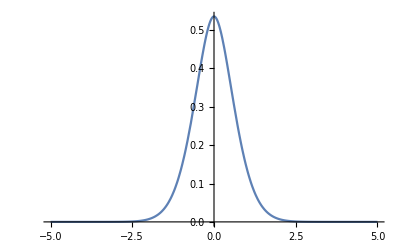

```mathematica
Plot[ψAiE[x,tabE[[1]]],{x,-5,5},PlotRange->All]
```

```mathematica
ψAiE[x_,e_]:=If[x>0,AiryAi[x/(1/(2m λ))^(1/3)-e/((λ^2/(2m))^(1/3))],AiryAi[-x/(1/(2m λ))^(1/3)-e/((λ^2/(2m))^(1/3))]]
ψAiO[x_,e_]:=If[x>0,AiryAi[x/(1/(2m λ))^(1/3)-e/((λ^2/(2m))^(1/3))],-AiryAi[-x/(1/(2m λ))^(1/3)-e/((λ^2/(2m))^(1/3))]]
```

```mathematica
D[ψAi[x,e],x]
```

((5 π)/2)^(1/3) AiryAiPrime[-5^(1/3) e (2/π)^(2/3)+((5 π)/2)^(1/3) x]

```mathematica
FindRoot[ψAi[0,e],{e,1.1,2}]
```

{e→1.84766}

```mathematica
normAiE=1/(√(Integrate[ψAiE[x,#]^2,{x,-∞,∞}]&/@tabE))
```

{3.97256,2.84412,2.57172}

```mathematica
Table[normAi[[i]]^2 Integrate[ψAiE[x,tabE[[i]]]^2 λ Abs[x],{x,-∞,+∞}],{i,3}]
```

{0.536724,1.71123,2.53934}

```mathematica
-1/(2m)Table[normAi[[i]]^2 Integrate[D[ψAiE[x,tabE[[i]]],x]^2,{x,-∞,+∞}],{i,3}]
```

{-0.268362,-0.855614,-1.26967}

```mathematica
%78-%79-tabE
```

{-1.97048×10^-10,-1.01018×10^-9,-2.9124×10^-9}

```mathematica
normAiO=1/(√(Integrate[ψAiO[x,#]^2,{x,-∞,∞}]&/@tabO))
```

{3.06303,2.67439,2.48246}

```mathematica
Table[normAiO[[i]]^2 Integrate[ψAiO[x,tabO[[i]]]^2 λ Abs[x],{x,-∞,+∞}],{i,3}]
```

{1.23177,2.15363,2.90836}

```mathematica
-1/(2m)Table[normAiO[[i]]^2 Integrate[D[ψAiO[x,tabO[[i]]],x]^2,{x,-∞,+∞}],{i,3}]
```

{-0.615885,-1.07681,-1.45418}

```mathematica
%%-%-tabO
```

{4.11005×10^-10,1.77001×10^-9,4.21607×10^-9}

```mathematica
tabE[[1]]
```

0.805086

```mathematica
Table[-1/(32 m^3)Integrate[Evaluate[Simplify@D[normAiE[[i]]ψAiE[x,tabE[[i]]],{x,2}]]^2,{x,-∞,∞}]+tabE[[i]],{i,3}]
```

{0.173445,0.552978,0.82056}

```mathematica
Table[-1/(32 m^3)Integrate[Evaluate[Simplify@D[normAiO[[i]]ψAiO[x,tabO[[i]]],{x,2}]]^2,{x,-∞,∞}]+tabO[[i]],{i,3}]
```

{0.39805,0.69593,0.939793}

```mathematica
Riffle[%%,%]
```

{0.173445,0.39805,0.552978,0.69593,0.82056,0.939793}

```mathematica
Riffle[%%,%]
```

{0.373416,0.85687,1.18996,1.49719,1.76483,2.02081}

```mathematica
Riffle[%%,%]
```

{0.792475,1.81352,2.49903,3.12609,3.66263,4.17223}

```mathematica
(1/{0.1714591057113921,0.39604977242515815,0.5509825585148747,0.6939299177723797,0.8185629681388491,0.9377961268883155})({0.17344478623055762,0.3980495447644169,0.5529778252725112,0.6959296117168643,0.8205595203621443,0.9397934446879758}-{0.1714591057113921,0.39604977242515815,0.5509825585148747,0.6939299177723797,0.8185629681388491,0.9377961268883155})
```

{0.0115811,0.0050493,0.00362129,0.00288169,0.00243909,0.0021298}